# Generate Hamiltonian of Carbon Ring (Fermions)

Find Adjacency Matrix and its Eigenvalues

```mathematica
Clear[n]
ClearSystemCache[]
```

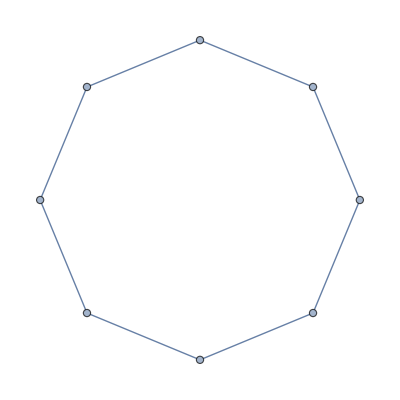

Adjacency Matrix is: (0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

Eigenvalues of Adjacency Matrix: {0.,-5.65685,-8.,-5.65685,0.,-5.65685,-8.,-5.65685}

Minimum Eigenenergy is: -19.3137

```mathematica
mix=0;
twist= 0;
t=If[twist>0,0.5,0];
c={{0,0},{1,0}};
ci[i_,n_] := Apply[KroneckerProduct,Join[Table[PauliMatrix[3],i-1],{c},Table[IdentityMatrix[2],n-i]]];
n=8; (*number of fermions*)
G = CycleGraph[n]
AM=AdjacencyMatrix[G];Print["Adjacency Matrix is: ",MatrixForm[AM]]
λ = N[Table[-4*Sqrt[4*(Sin[2*π*(m+t)/n])^2],{m,0,n-1}]]  (*or Abs[N[Eigenvalues[-AM]]] *); Print["Eigenvalues of Adjacency Matrix: ", λ]
CC[i_]:=λ[[i]]( ConjugateTranspose[ci[i,n]].ci[i,n]-(0.5*IdentityMatrix[Length[ci[i,n]]]));
CCmix[i_,j_]:=If[mix>0,ConjugateTranspose[ci[i,n]].ci[j,n],0];
Cmix=∑_(j=1)^n ∑_(i=1)^n If[i≠j,CCmix[i,j],0];
H=N[∑_(i=1)^n (CC[i]) + Cmix]; (* Print["Hamiltonian is: ", MatrixForm[H]] *)
en = Eigenvalues[H];Print["Minimum Eigenenergy is: ", Min[en]]
```

Export Hamiltonian to File

```mathematica
SetDirectory[NotebookDirectory[]];
name =StringDelete[CurrentValue["NotebookFileName"],".nb"];
Export["../Hams/"<>name<> If[mix>0,"Mix",""]<> If[t>0,"twist","Periodic"]<> ToString["_"] <> ToString[n] <> ".txt",H,"Table"]
```

../Hams/FermionRingPeriodic_8.txt